```mathematica
SetDirectory[NotebookDirectory[]];
```

Version

```mathematica
version=1;
lattName="lattice_v"<>IntegerString[version,10,2]<>"/";
```

Particle counts

```mathematica
a=Import[lattName<>"counts/A.txt","Table"];
b=Import[lattName<>"counts/B.txt","Table"];
c=Import[lattName<>"counts/C.txt","Table"];
```

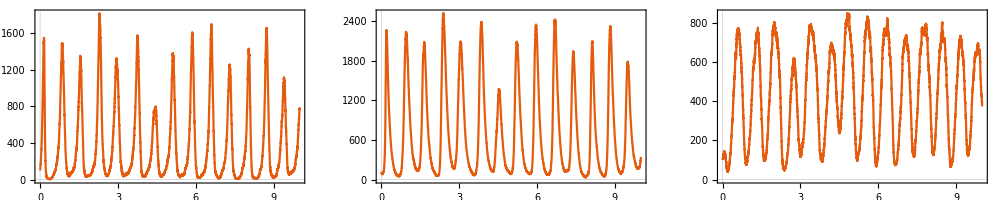

```mathematica
GraphicsRow[{
ListLinePlot[a],
ListLinePlot[b],
ListLinePlot[c]
},ImageSize->1000]
```

```mathematica
dat=Transpose[{a[[;;,2]],b[[;;,2]],c[[;;,2]]}];
Show[ListPointPlot3D@dat,Graphics3D@Line@dat]
```

-Graphics3D-

NN counts

```mathematica
aa=Import[lattName<>"nns/A_A.txt","Table"];
ab=Import[lattName<>"nns/A_B.txt","Table"];
ac=Import[lattName<>"nns/A_C.txt","Table"];
bb=Import[lattName<>"nns/B_B.txt","Table"];
bc=Import[lattName<>"nns/B_C.txt","Table"];
cc=Import[lattName<>"nns/C_C.txt","Table"];
```

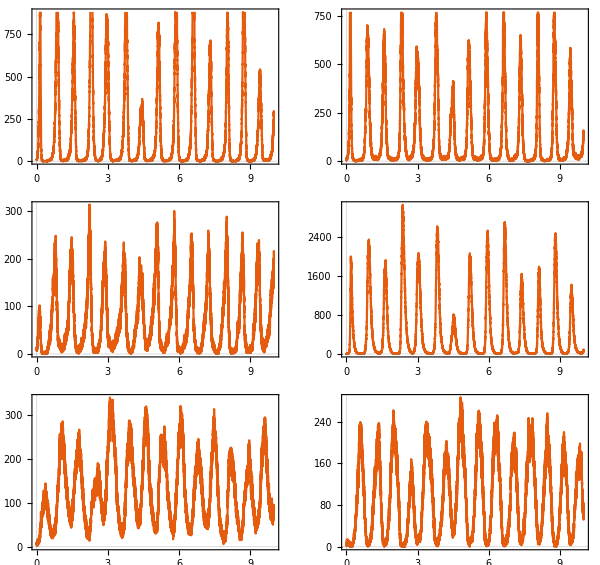

```mathematica
GraphicsGrid[{{
ListLinePlot[aa],
ListLinePlot[ab]},
{ListLinePlot[ac],
ListLinePlot[bb]},
{ListLinePlot[bc],
ListLinePlot[cc]}
},ImageSize->600]
```

```mathematica
dat=Transpose[{aa[[;;,2]],ab[[;;,2]],ac[[;;,2]]}];
Show[ListPointPlot3D@dat,Graphics3D@Line@dat]
```

-Graphics3D-

```mathematica
dat=Transpose[{ab[[;;,2]],bb[[;;,2]],bc[[;;,2]]}];
Show[ListPointPlot3D@dat,Graphics3D@Line@dat]
```

-Graphics3D-

Lattice

### Visualize a lattice

```mathematica
makeColDict[species_]:=Module[
{colDict,cols,colVal}
,
colDict=Association[];
cols=Sort[species];
colVal=0.0;
Do[
colDict[col]=ColorData["BrightBands"][colVal];
If[col≠cols[[-1]],
colVal+=1.0/(Length[cols]-1);
];
,{col,cols}];
Return[colDict];
]
```

```mathematica
visualizeLattice[lattice_,boxLength_,colDict_]:=Graphics3D[Table[{EdgeForm[],colDict[l[[4]]],Cuboid[l[[;;3]]]},{l,lattice}],Background->Black];
```

### Lattice

#### Box len

```mathematica
boxLength=20;
```

#### Viz

```mathematica
colDict=makeColDict[{"A","B","C"}];
```

```mathematica
colDict
```

<|A→RGBColor[0.90222, 0.101808, 0.198306],B→RGBColor[0.23499123809468608, 0.9676036067435916, 0.1156329799245431],C→RGBColor[1., 0.749752, 0.501183]|>

```mathematica
colDict=Association[];
colDict["A"]=RGBColor[0.81,0.0,0.79];
colDict["B"]=RGBColor[1.0,0.78,0.49];
colDict["C"]=RGBColor[0.52,0.96,1.0];
```

```mathematica
colDict
```

<|A→RGBColor[0.81, 0., 0.79],B→RGBColor[1., 0.78, 0.49],C→RGBColor[0.52, 0.96, 1.]|>

```mathematica
Manipulate[
latt=Import[lattName<>"lattice/"<>IntegerString[i,10,4]<>".txt","Table"];
visualizeLattice[latt,boxLength,colDict]
,{i,1,1001,1}]
```

```mathematica
Monitor[
Do[
Do[
latt=Import[lattName<>"lattice/"<>IntegerString[j*100+i,10,4]<>".txt","Table"];
img=Image[visualizeLattice[latt,boxLength,colDict],ImageResolution->200];
Export[lattName<>"images/"<>IntegerString[j*100+i,10,4]<>".jpg",img];
,{i,0,99}];
,{j,4,9}];
,{
ProgressIndicator[j,{0,9}],ProgressIndicator[i,{0,99}]}]
```